## Integrate the cell velocities obtained from solving system of PDEs

## Load data

```mathematica
(* Load data *)
(*RootFolder =FileNameJoin[{NotebookDirectory[], "Plots_model4b_FD_solver/simulation_set4_try_kD_profiles/3c_gaussian_shifted_right/"}];*)
(*RootFolder =FileNameJoin[{NotebookDirectory[], "Plots_model4b_FD_solver/simulation_set3/sim4b3_higher_friction/"}];*)
RootFolder =FileNameJoin[{NotebookDirectory[], "Plots_model4b_FD_solver/simulation_set3/"}];

ρAll =Transpose@Import[FileNameJoin[{RootFolder, "data_rho_1.csv"}]];
ϕAll=Transpose@Import[FileNameJoin[{RootFolder, "data_phi_1.csv"}]];
VAll = Transpose@Import[FileNameJoin[{RootFolder, "data_V_1.csv"}]];
params= Import[FileNameJoin[{RootFolder, "data_parameters.csv"}]]
```

{{eO,1000},{eM,30},{η,25/9},{ξ,0.28},{τ,10},{D1,15},{α,1/100000},{ρdA,0.0058},{ρdB,0.0076},{ρh,1/1000},{aρ,2},{a,6},{L,1500},{tmax,8},{Nx,100},{T,100}}

```mathematica
(*Define mesh*)
Nx=100;
T= 100;
tmax=8;
L=1500;
ΔxSet = 2L/(Nx);
ΔtSet = tmax/T;
xmesh= Range[-L, L, ΔxSet];
tmesh =Range[0, tmax, tmax/T];
Print[xmesh[[Nx/2+1]]];
Print[ N@ΔxSet]
Print[ N@ΔtSet]
```

0

30.

0.08

## Integrate V

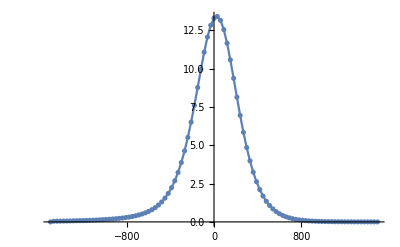

```mathematica
(* Interpolation function*)
idx =1;
dataTmp =Transpose[{xmesh, VAll[[idx,;;]]}];
InterpolationV =Interpolation[ dataTmp, InterpolationOrder->1];
p1=ListPlot[dataTmp ];
p2=Plot[InterpolationV[x], {x, -L , L}];
Show[p1, p2, PlotRange-> All]
```

### Simulate 1 cell

Initial positions to take: 0, -200, -400 μm, corresponding to the locations of the tracked cells

```mathematica
(*Settings*)
IntOrder=1; (*interpolation order*)
xCell0List = {0, -200, -400};
(*sim=1;*)

For[sim=1, sim< 4,sim++,
Print[sim];

(* interpolation func*)
xCell0 = xCell0List[[sim]]; (*initial position of tracked cell*)
tIdx =1;
dataTmp =Transpose[{xmesh, VAll[[tIdx,;;]]}];
InterpolationV0 =Interpolation[ dataTmp, InterpolationOrder->IntOrder];
vCell0=InterpolationV0[xCell0];
xCellAll={xCell0};
vCellAll={vCell0};
For[tIdx=2, tIdx≤ T+1, tIdx++,
xCellTmp = xCellAll[[-1]];
vCellTmp=vCellAll[[-1]];
xCellNew =xCellTmp+vCellTmp*ΔtSet;

(* define new interpolation func*)
dataTmp =Transpose[{xmesh, VAll[[tIdx,;;]]}];
InterpolationVTmp =Interpolation[ dataTmp, InterpolationOrder->IntOrder];
vCellNew = InterpolationVTmp[xCellNew];

(* add results to lists *)
AppendTo[xCellAll, xCellNew];
AppendTo[vCellAll, vCellNew];
];

(* Save results *)
settingsToSave={{"xCell0", xCell0},{"IntOrder", IntOrder}};
Export[FileNameJoin[{RootFolder, StringJoin["1cell_sim",ToString[sim],"_xCellAll.csv"]}], xCellAll, "CSV"];
Export[FileNameJoin[{RootFolder, StringJoin["1cell_sim",ToString[sim],"_vCellAll.csv"]}], vCellAll, "CSV"];
Export[FileNameJoin[{RootFolder, StringJoin["1cell_sim",ToString[sim],"_settings.csv"]}], settingsToSave, "CSV"];
]
```

1

2

3

```mathematica
(*
ListPlot[Transpose[{tmesh,xCellAll }] ]
ListPlot[Transpose[{tmesh,vCellAll }] ]
*)
```

```mathematica
(* For troubleshooting *)
(*
tIdx=2;
xCellTmp=xCellAll[[-1]];
vCellTmp=vCellAll[[-1]];
xCellNew=xCellTmp+vCellTmp*ΔtSet;
(* define new interpolation func*)
dataTmp=Transpose[{xmesh, VAll[[tIdx,;;]]}];
InterpolationVTmp=Interpolation[ dataTmp, InterpolationOrder->IntOrder];
vCellNew=InterpolationVTmp[xCellNew];
*)
```